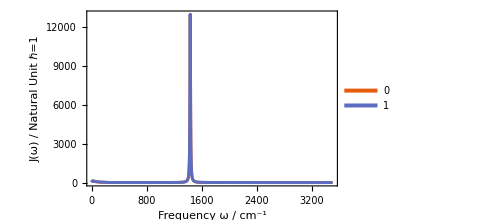

```mathematica
freq={0.701881466027484,1.410637263718584,2.1265071756304073,2.8497153146080616,3.5804720172708033,4.318974934643464,5.065410523706402,5.819955990235091,6.5827815169222506,7.35405258289592,8.133932214735689,8.922583060649977,9.720169229174024,10.526857873258546,11.34282052802745,12.16823422696225,13.003282429309346,13.84815579371954,14.703052831715201,15.568180471248244,16.44375455648542,17.330000305751543,18.227152745685693,19.135457136293297,20.05516939878096,20.986556555815543,21.929897192098764,22.88548194183491,23.85361400871107,24.83460972335062,25.828799142785712,26.836526696276756,27.858151881753557,28.894050017233244,29.944613051768762,31.01025044078037,32.09139009101674,33.188479380871996,34.30198626235598,35.4324004516743,36.58023471612986,37.746026265917614,38.93033826035863,40.13376143922209,41.35691589103392,42.600452971685,43.865057388258734,45.15144946482178,46.46038760900332,47.792671000557704,49.14914252582531,50.53069198511675,51.93825960363024,53.372839880637024,54.83548581644451,56.32731356217751,57.84950754384742,59.40332611967764,60.99010783842022,62.61127837668481,64.26835824541017,65.962971369907,67.69685466485383,69.47186874579468,71.29000994277622,73.15342381064971,75.06442036535519,77.02549131759308,79.03932962644167,81.1088517579541,83.2372231104679,85.427887163031,87.6845990208746,90.01146417864616,92.41298350661273,94.89410569852029,97.46028871738388,100.1175721576992,102.87266293748449,105.73303738001698,108.7070635973965,111.80414922296107,115.03492106711525,118.41144535110755,121.94750004123571,125.65891481452707,129.5639998735566,133.6840930271756,138.0442664885864,142.67425285867762,147.60967733245064,152.89372640493363,158.57945307295765,164.73303456615736,171.43849897712087,178.80479837394859,186.97679289387088,196.15311229125822,206.61706612948598,218.79658431895913,1432.882948413672};
coup={-3.67810533,5.17717879,6.28661045,-7.17290114,-7.90101665,-8.50580348,-9.00977319,-9.42933577,9.77740447,10.06461364,10.29994293,10.49107012,10.64459422,10.76619404,-10.86075271,-10.93246204,-10.98491339,-11.02117785,-11.04387724,11.05524676,11.05718999,11.05132676,11.03903478,11.0214854,-10.9996744,-10.97444829,-10.94652677,-10.91652181,-10.88495392,10.85226593,10.81883469,10.784981,10.75097804,-10.71705853,-10.6834208,-10.65023396,-10.6176423,10.58576904,10.55471951,10.52458391,10.49543965,-10.4673533,-10.4403824,-10.41457689,-10.38998039,10.36663136,10.344564,10.32380918,-10.30439508,-10.28634795,-10.26969262,-10.25445305,10.2406528,10.22831549,10.21746513,-10.20812657,-10.20032583,10.19409044,10.18944978,10.18643545,-10.18508158,-10.18542519,10.18750659,10.19136974,-10.1970627,-10.20463807,10.21415351,10.22567226,-10.23926377,-10.25500438,10.2729781,10.29327746,-10.31600448,10.34127184,-10.36920408,10.39993916,-10.43363009,10.47044691,-10.51057897,10.55423756,-10.60165902,10.65310833,-10.70888329,10.7693195,-10.83479605,10.90574218,-10.98264477,11.0660568,-11.1566061,11.25500357,-11.36204839,11.47862474,-11.60567782,11.74414082,-11.89474363,12.05752149,-12.23048919,12.40562774,-12.55380294,12.5354662,452.28598404};
j1[ω_,ωi_,Δ_,ki_]:=ki^2/ωi(ω Δ/Pi)/((ω-ωi)^2+Δ^2);
j0[ω_,ωi_,Δ_,ki_]:=ki^2(Δ/Pi)/((ω-ωi)^2+Δ^2);
j2[ω_,ωi_,Δ_,ki_]:=ki^2/ωi^2(ω^2 Δ/Pi)/((ω-ωi)^2+Δ^2);
delta=5;
DASD=Plot[{
Sum[j0[w,freq[[n]],delta,coup[[n]]],{n,1,Length[freq]}],
Sum[j1[w,freq[[n]],delta,coup[[n]]],{n,1,Length[freq]}]},
{w,0,3500},
PlotRange->{All,All},
PlotStyle->Thickness[0.006],
PlotTheme->"Scientific",
GridLines->None,
LabelStyle->{FontFamily->"LM Sans",12},
FrameStyle->Thickness[0.006],
PlotLegends->Placed[LineLegend[{"0","1","2"},LegendFunction->None,LegendMargins-> -1,Spacings->{.1,0.0},LegendMarkerSize->Small,LegendMargins->0,LegendLayout->{"Column",1}],{0.15,0.85}],
FrameLabel->{"Frequency ω / cm^-1","J(ω) / Natural Unit ℏ=1"}]
```

```mathematica
Sum[coup[[n]]^2/freq[[n]],{n,1,Length[freq]}]
```

599.754

```mathematica
NIntegrate[Sum[j1[w,freq[[n]],1,coup[[n]]],{n,1,Length[freq]}]/w,{w,0,100000},MaxRecursion->100]
```

574.949

```mathematica
j2[x,ωi,Δ,ki]
```

(ki^2 x^2 Δ)/(π (Δ^2+(x-ωi)^2) ωi^2)

```mathematica
j1[ω,ωi,Δ,ki]
```

(ki^2 Δ ω)/(2 π (Δ^2+(ω-ωi)^2) ωi)

```mathematica
Integrate[1/(2 ωi^3)(ω^3 Δ/Pi)/((ω-ωi)^2+Δ^2)/.{Δ->1.2,ωi->10},{ω,-1000,1000}]//N
```

8.11633

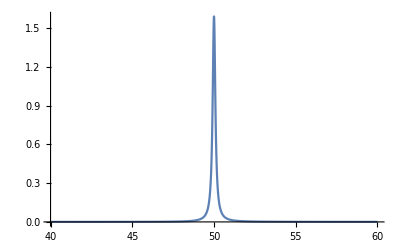

```mathematica
func={1/(2 ωi^2)(ω^2 Δ/Pi)/((ω-ωi)^2+Δ^2),1/(2 ωi)(ω Δ/Pi)/((ω-ωi)^2+Δ^2),1/2(Δ/Pi)/((ω-ωi)^2+Δ^2)};
Plot[func[[1]]/.{Δ->0.1,ωi->50},{ω,40,60},PlotRange->{Automatic,All}]
```